```mathematica
SetDirectory[NotebookDirectory[]];
mat2 = Import["Displacements.txt","Table"];
```

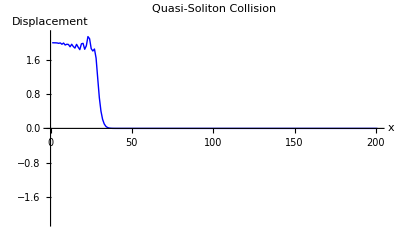

```mathematica
ListPlot[mat2[[All,100]],PlotRange-> {-2.2,2.2}, PlotStyle-> Blue,Joined->True,AxesLabel-> {x,Displacement},PlotLabel->"Quasi-Soliton Collision"]
```

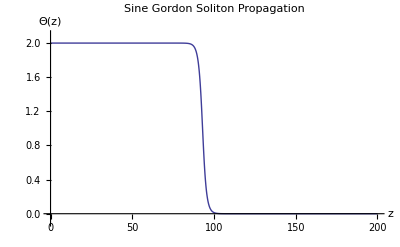

```mathematica
v = 2.835; (*Computed from the x-t diagram*)
co =√10; 
wo=(π*0.264911)^0.5; (*Max amplitude in Sine fit*)
u[z_] := 4/π ArcTan[Exp[-wo/co (z-93)/(√(1-(v/co)^2))]]
Plot[u[z],{z,0,200},PlotRange-> {-0.1,2.1}, PlotLabel->"Sine Gordon Soliton Propagation", AxesLabel-> {z,Θ[z]}]
```

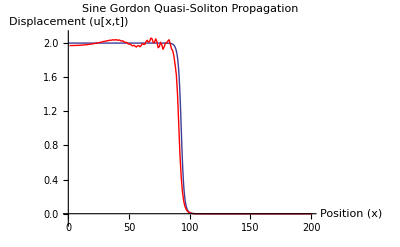

```mathematica
Needs["PlotLegends`"]
Show[Plot[u[z],{z,0,200},PlotRange-> {-0.1,2.1}, PlotLabel->"Sine Gordon Quasi-Soliton Propagation", AxesLabel-> {"Position (x)","Displacement (u[x,t])"}],ListPlot[mat2[[All,327]],Joined->True,PlotRange-> {-0.1,2.2}, PlotStyle-> Red,AxesLabel-> {"Position (x)","Displacement (u(x,t))"},PlotLabel->"Sine Gordon Quasi-Soliton Propagation at a certain time instant"]]
```

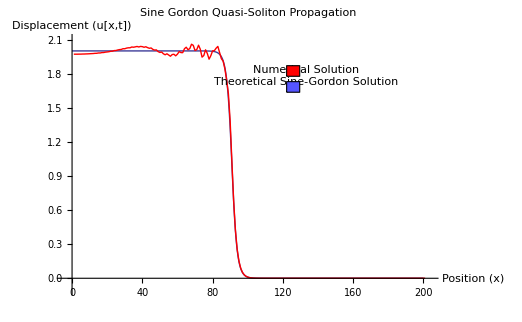

```mathematica
v=2.835/10;
```

```mathematica
A =ListContourPlot[Transpose[mat2],Axes-> True, FrameLabel-> {"Position(x)", "Time(t)"},PlotLabel-> "X-T contour plot of displacements",PlotLegends->Automatic];
```

```mathematica
B = Plot[x/v,{x,1,200},PlotStyle-> {Red,Thick}];
```

```mathematica
Show[A,B]
```

-Graphics-

```mathematica
plots=Table[ListPlot[mat2[[All,2i]],Joined->True,PlotRange-> {-2.2,2.2}],{i,1,170}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
Export["collision_animation.avi",plots]
```

collision_animation.avi